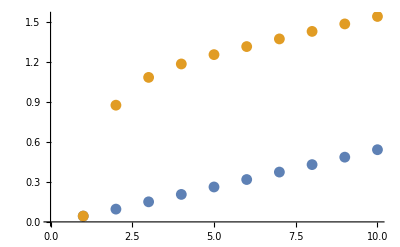

```mathematica
(*ISOTERMAL*)
Module[{tf,Ac,T,Fao,P,k,R,n,Qo,s1,acc,vel,x1,x2,rtBound,p1,p2,Δ},
tf=10;
(*Ac=π/4*(0.25)^2;*)
T=400;
Fao=0.5;
P=5;
k=0.1*Exp[-(1.16*10^4)/(8.314*(T+273))];
R=8.314*10^-5;
n=2;
Qo=(R*(T+273))/P*Fao;


s1=NDSolve[{
Na'[t]==-(k*Na[t])/Q[t],
Nb'[t]==n*(k*Na[t])/Q[t],
Q'[t]==(-(k*Na[t])/Q[t]+n*(k*Na[t])/Q[t])*(R*(T+273))/P,
Na[0]==Fao,Nb[0]==0,Q[0]==Qo},{Na,Nb,Q},{t,0,tf}];

acc=Table[10*(Q[t]-Q[t-1])/.s1,{t,1,tf}];
vel=Table[Sum[acc[[i]],{i,1,t}],{t,1,tf}];
x1=Flatten@Table[Sum[vel[[i]],{i,1,t}],{t,1,tf}];
x2=Flatten@Table[x1[[i]]+(Q[i-1]/Q[0]-1)/.s1,{i,1,Length[x1]}];

(*rtBound=x1[[Length[x1]]]+(Q[Length[x1]-1]/Q[0]-1)/.s1[[1]];*)

(*Graphics[{
Rectangle[{Interpolation[x1],0},{Interpolation[x2],0.25}]
},PlotRange->{{0,rtBound},{0,0.25}}]*)

ListPlot[{x1,x2}]

]
```

```mathematica
{{0.043642336795003914},{0.09589111268878354},{0.15066740884142205},{0.2062408881973539},{0.2620709892000722},{0.31798422998860726},{0.3739244613423426},{0.4298734607105077},{0.4858253091912415},{0.5417780835098988}}
```

```mathematica
{{{0.043642336795003914}},{{0.8758701164888134}},{{1.0844613154973683}},{{1.1852068199638988}},{{1.2552842369082802}},{{1.3157838383528495}},{{1.373209949979727}},{{1.4296413266838204}},{{1.4857498777534281}},{{1.5417535716182469}}}
```

```mathematica
(*time = 100;
T =700;
R = 0.00008314;
k = 0.1;
Ureac = 0.41600;
order = 2;
PGas = 5;
Ao =1;
Vo = Ao*R*T/PGas;
VelO = 1;
VolInitial = 3000;

Rate = k*Exp[-Ureac/(R*T)];
s=NDSolve[{
A'[t] == -Rate*A[t]/V[t],
B'[t] == order*Rate*A[t]/V[t],
V'[t] == ( (-Rate*A[t]/V[t])+(order*Rate*A[t]/V[t]))*R*T/PGas,A[0]==Ao, B[0]==0,V[0]==Vo},{A,B,V},{t,0,time}];*)

(*ListPlot[{Flatten[Distance1],Flatten[Distance2]}]*)
```

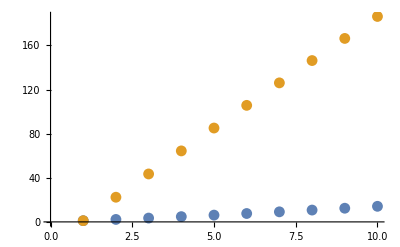

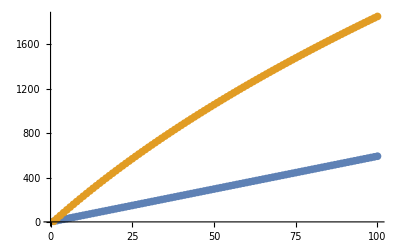

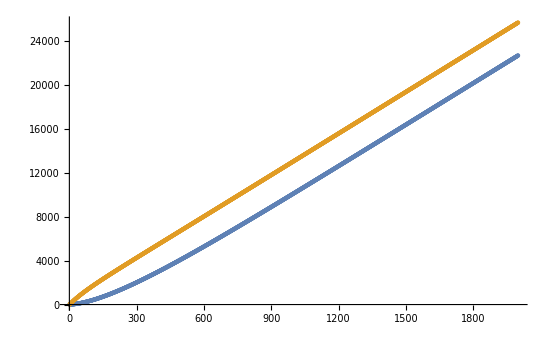

```mathematica
(8.314*10^-5*(400+273))/5*0.5
```

0.00559532

```mathematica
Table[{i}-{i-1},{i,1,10}]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}